```mathematica
ClearAll["Global`*"]
```

```mathematica
(*This code considers a first order phase transformation potential and plots the Order parameter as a function of temperature. We also present a way to copute the stress vs transition temperature diagram along with the free energy minimization visualization.*)
```

```mathematica
(*Specifying some parameters*)
```

```mathematica
XL:=-30;
XR:=40
h[x_,T_]:=x^4/4-10*x^3-T*(x-20)^2
Manipulate[Plot[h[x,T],{x,XL,XR}],{T,0,200}]
```

```mathematica
L[x_,s_]:=s*x
(*bartab=Table[{i},{i,XL,XR,1}];
Manipulate[Soln=NMinimize[{h[x,T]-L[x,s]},x,Method->{"Automatic","InitialPoints"->bartab}];{Plot[{s*y+Soln[[1]],h[y,T]},{y,XL,XR},AxesLabel->{"x","h(x)"},PlotRange->{-250000,200000},ImageSize->Large],"Min at ",x/.Last[Soln]},{T,0,200},{{s,0},-20000,20000}]*)
```

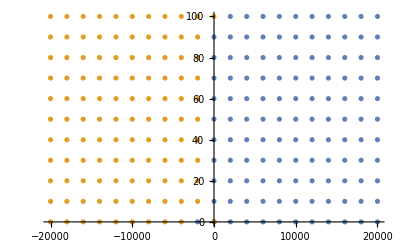

```mathematica
pL={{0,0}};
pR={{0,0}};
bartab2=Table[{i},{i,XL,XR,5}];
For[s=-20000,s<=20000,s=s+2000,For[T=0,T≤100,T=T+10,Soln2=NMinimize[{h[x,T]-L[x,s]},x,Method->{"Automatic","InitialPoints"->bartab}];y=x/.Last[Soln2];If[y>=0,AppendTo[pR,{s,T}],AppendTo[pL,{s,T}]]]]
ListPlot[{pR,pL},PlotRange->Automatic]
```